```mathematica
Clear["Global`*"];
```

```mathematica
<</home/xierr/.Mathematica/Applications/CustomTicks/CustomTicks.m
```

```mathematica
tlen=0.014;tickd=In;thick=Thickness[0.002];ip={{80,30},{60,30}};
```

```mathematica
cliprange[points_List,xmax_:4.99]:=Module[{xmaxpos},xmaxpos=Position[points,Nearest[points[[All,1]],xmax][[1]]][[1,1]];
points[[1;;xmaxpos]]];
```

```mathematica
(*NND fitting formular*) 
ξsb[ξb_?NumericQ]:=Gamma[ξb+1/2]/Gamma[ξb];
pp[s_,ξb_]:=1/Gamma[1/2+ξb]^2 2^(-1-2 ξb) Gamma[ξb] Gamma[2+2 ξb] HypergeometricU[1+ξb,1/2,(s^2 Gamma[ξb]^2)/(4 Gamma[1/2+ξb]^2)];
```

```mathematica
nnd1=cliprange[Import["A2ASS6_DNA_NND.txt","Table"]];
nnd2=cliprange[Import["Q8WXI7_DNA_NND.txt","Table"]];
nnd3=cliprange[Import["Q8WZ42_DNA_NND.txt","Table"]];
nnd4=cliprange[Import["Q9I7U4_DNA_NND.txt","Table"]];
```

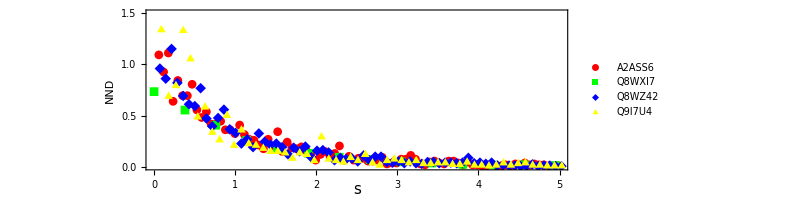

```mathematica
nndpoints=ListPlot[{nnd1,nnd2,nnd3,nnd4}(*use your data*),PlotRange->{{0,5},{0,1.5}},AspectRatio->1/3.,ImageSize->600,PlotMarkers->Automatic,Frame->True,PlotStyle->{Red, Green, Blue, Yellow},
(*********************Frame Ticks***********************)
ImagePadding->ip,PlotRangeClipping->False,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[{0,0.5,1,1.5},{0.25,0.75,1.25},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,TickDirection->tickd],(*left*)
LinTicks[{0,0.5,1,1.5},{0.25,0.75,1.25},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[{0,1,2,3,4,5},{0.5,1.5,2.5,3.5,4.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],(*down*)
LinTicks[{0,1,2,3,4,5},{0.5,1.5,2.5,3.5,4.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}},(*up*)FrameLabel->{None,Style["NND",FontFamily->"Times",Italic,15]},
(***************************************)PlotLegends->Placed[PointLegend[Automatic,Style[#,12,FontFamily->"Times"]&/@{"A2ASS6","Q8WXI7","Q8WZ42","Q9I7U4"},LegendFunction->Framed,LegendMargins->0],{(*legend position*)Scaled[0.85],Scaled[0.5]}],Epilog->{Text[Style["StyleBox[\"s\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times"],Scaled[{0.5,-0.12}]]}]
```

```mathematica
nlm1=NonlinearModelFit[nnd1,pp[s,ξb],ξb,s]
```

FittedModel[2.18955 HypergeometricU[«19»,«1»,«20» «1»]]

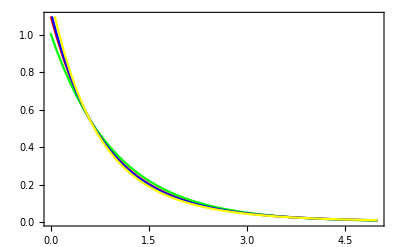

```mathematica
nndmat=Plot[{pp[s,2.45],pp[s,23.435],pp[s,2.03],pp[s,1.328]},{s,0,5},PlotRange->{{0,5},{0,1.1}},PlotStyle->{Red, Green, Blue, Yellow},Frame->True]
```

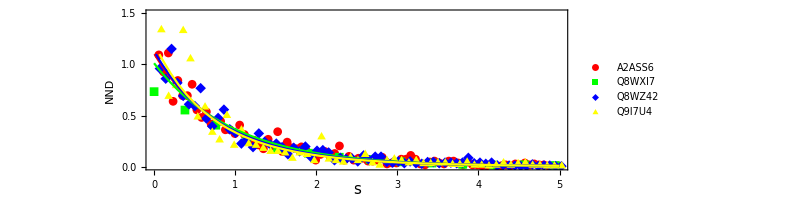

```mathematica
p1=Show[nndpoints,nndmat]
```

```mathematica
NV[L_?NumericQ,ξb_?NumericQ]:= L+((ξsb[ξb]/(√ξb))^-2-1) L^2;
```

```mathematica
nv1=Import["A2ASS6_DNA_variance.txt","Table"];
nv2=Import["Q8WXI7_DNA_variance.txt","Table"];
nv3=Import["Q8WZ42_DNA_variance.txt","Table"];
nv4=Import["Q9I7U4_DNA_variance.txt","Table"];
```

```mathematica
nvpoints=ListPlot[{nv1,nv2,nv3,nv4}(*use your data*),PlotRange->{{0,150},{0,4000}},DataRange->{{0,150},{0,4000}},AspectRatio->1/3.(*specify the height-to-width ratio*),ImageSize->600,PlotMarkers->Automatic,Frame->True,PlotStyle->{Red, Green, Blue, Yellow},
(*********************Frame Ticks***********************)
ImagePadding->ip,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[Range[0,4000,1000],Range[500,3500,500],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,TickDirection->tickd],(*left*)
LinTicks[Range[0,4000,1000],Range[500,3500,500],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[Range[0,150,50],Range[25,125,25],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],(*down*)
LinTicks[Range[0,150,50],Range[25,125,25],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}},(*up*)FrameLabel->{Style["StyleBox[\"L\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times"],Style["NV",FontFamily->"Times",Italic,15]}];
```

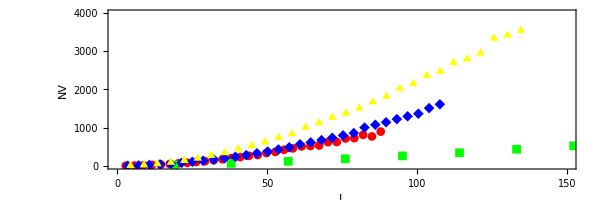

```mathematica
Show[nvpoints]
```

```mathematica
nlm1=NonlinearModelFit[nv1,NV[L,ξb],ξb,L];
nlm2=NonlinearModelFit[nv2,NV[L,ξb],ξb,L];
nlm3=NonlinearModelFit[nv3,NV[L,ξb],ξb,L];
nlm4=NonlinearModelFit[nv4,NV[L,ξb],ξb,L];
```

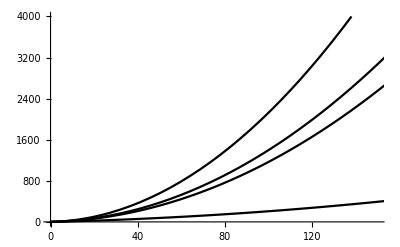

```mathematica
nvcurv=Plot[{Normal[nlm1],Normal[nlm2],Normal[nlm3],Normal[nlm4]},{L,0,225},PlotStyle->Black,PlotRange->{{0,150},{0,4000}}]
```

```mathematica
p3=Show[nvpoints,nvcurv,(*we want nvcurv as background*)Epilog->{Text[Style["λ = 2.45",FontSize->13,FontFamily->"Times"],Scaled[{0.89,0.35}]],
Text[Style["λ = 23.435",FontSize->13,FontFamily->"Times"],Scaled[{0.75,0.2}]],
Line[{Scaled[{0.58,0.05}],Scaled[{0.65,0.18}]}],
Text[Style["λ = 2.03",FontSize->13,FontFamily->"Times"],Scaled[{0.85,0.7}]],
Line[{Scaled[{0.86,0.65}],Scaled[{0.9,0.6}]}],
Text[Style["λ = 1.328",FontSize->13,FontFamily->"Times"],Scaled[{0.46,0.4}]],
}]
```

-Graphics-

```mathematica
p=Column[{p1,p3},Spacings->-3.5]
```

-Graphics-

```mathematica
Export["DNA_new.eps",p]
```

DNA_new.eps